# Slightly Advanced Introduction to Mathematica.

Below is a slightly advanced introduction to some concepts in Mathematica.  You may be familiar with most of them.

Initializing the kernel:

On the right hand side there are a number of brackets,  Click on the one that is beside the expression "2+2".  Then press the return key and the shift key simultaneously.  This will start  up the Mathematica "kernel" or central processing program.  It  may take a few seconds to respond.

```mathematica
2+2
```

4

Complicated calculator:

Mathematica can do more than evaluate 2+2.  Click on the bracket to the right of each of the following expressions and  again press "shift-return".

```mathematica
4 3^6-28 7^2
```

1544

```mathematica
(234 128-48 632)/54^2
```

-32/243

```mathematica
Sin[π/6]^4+Cos[π/4]^2
```

9/16

```mathematica
100!
```

93326215443944152681699238856266700490715968264381621468592963895217599993229915608941463976156518286253697920827223758251185210916864000000000000000000000000

```mathematica
√15241578750190521
```

123456789

In Mathematica adjacent terms are multiplied (you don't have to explicitly put in a multiplication symbol).  To raise something to a power, you can either use the caret "^" symbol, or use the BasicInput palette and typeset an exponent.  (Select the "Palette" submenu from the "File" menu).   Thus:

                            x^2 = x^2

   Also note that we have functions like Sqrt[...] for taking the square root, and sines and cosines are Sin[] and Cos[].  The capital letters are important, as are the square brackets.  All predefined functions in Mathematica are capitalized, and take square brackets.  The curly brackets {} are used to separate  parameters, or to mark elements as belonging to a list.  The  program will whine petulantly and refuse to work if you use  the wrong brackets in the wrong place, or forget a comma when  it wants one there.

### The most important point in this whole presentation:

One extremely important point: highlight the word "Sin" above in the input box.  Now pull down the help menu and select "Find Selected Function".  This will tell you all about the sine function in Mathematica.  The help browser in Mathematica is extensive and extremely helpful.  You can look up functions alphabetically in its index or browse them by subject. You can take a tour of Mathematica and see what it can do.  You can see thousands of examples.  Learn to use the browser.

### Mathematica is a Symbolic manipulator:

Mathematica is a symbolic manipulator.  It does not always evaluate things in a way you might expect!  Below are two  examples.  In each case we as Mathematica to evaluate an  expression.  If we want a decimal or NUMERICAL answer, we have  to use the  function N[...], which calculates its argumument in a numerical fashion.

```mathematica
14/6
```

7/3

```mathematica
N[14/6]
```

2.33333

```mathematica
√68
```

2 √17

```mathematica
N[√68]
```

8.24621

```mathematica
√68.
```

8.24621

Mathematica and algebra

Mathematica is more than just a fancy calculator.  It can perform algebraic operations as well.  The form or "syntax"   is:

Solve[{eq1==rhs1,eq2==rhs2,...},{var1,var2..}]

Note the funny double equal signs (==).  This is used because we are specifying a symbolic relationship, we're not just renaming the eq1 by rhs1.   There are a few examples below.  Again, click on the bracket  on the RHS and hit shift-enter.
  
  A quadratic equation:

```mathematica
Solve[{x^2+x-12==0},{x}]
```

{{x→-4},{x→3}}

A cubic equation:

```mathematica
Solve[{x^3-3 x^2+x+1==0},{x}]
```

{{x→1},{x→1-√2},{x→1+√2}}

Even a quartic equation!

```mathematica
Solve[{x^4+x^3-4 x^2-x+1==0},{x}]
```

{{x→-1-√2},{x→-1+√2},{x→1/2 (1-√5)},{x→1/2 (1+√5)}}

You can also solve systems of equations this way:

```mathematica
Solve[{x+y == 12, 4x-2y== 24},{x, y}]
```

{{x→8,y→4}}

However this is not the recommended way for large systems of equations - use

## Integrals:

Mathematica can do integrals symbolically.   Here's an integral you probably don't want to do by hand:

```mathematica
Integrate[Sin[x]/x,{x,0,Infinity}]
```

π/2

Mathematica can do this integral numerically.

```mathematica
NIntegrate[Sin[x]/x,{x,0,Infinity}]
```

1.5708

The point is that Mathematica can also do integrals that have no hope of being done analytically:

```mathematica
NIntegrate[BesselJ[0,x]^2 Sqrt[1/(1+x^2)] ,{x,0,1}]
```

0.761681

## Vectors and Matrices:

The fundamental item in Mathematica is the "list."   This is much like a vector. It consists of a set of elements  enclosed in curly brackets:  "{a1, a2, a3...}".    We can construct a list either by hand, or by having Mathematica perform some action repeatedly using the Table command.  The latter is much like a "do-loop" in Fortran or a "for-next" loop in Basic.

```mathematica
vector1={1,2,3,4}
vector2=Table[n!,{n,1,20}]
```

{1,2,3,4}

{1,2,6,24,120,720,5040,40320,362880,3628800,39916800,479001600,6227020800,87178291200,1307674368000,20922789888000,355687428096000,6402373705728000,121645100408832000,2432902008176640000}

When working with vectors and matrices, it is important to know when to tell Mathematica to shut up.  If you put a semicolon on the end of a line, then the calculation is performed, but the output is suppressed.

```mathematica
vector1={1,2,3,4};
vector2=Table[n!,{n,1,20}];
```

If you want a pretty version of the vector, then use MatrixForm.

```mathematica
MatrixForm[vector2]
```

(1
2
6
24
120
720
5040
40320
362880
3628800
39916800
479001600
6227020800
87178291200
1307674368000
20922789888000
355687428096000
6402373705728000
121645100408832000
2432902008176640000)

To refer to an element in the list, we just double square brackets.  For example, the 10th element in vector2 is vector2[[10]]:

```mathematica
vector2[[10]]
```

3628800

A matrix is just a list of lists.  Again, we can write it out by hand or have Mathematica create it using a Table command.

```mathematica
matrix1={{1,2,3,4},{5,0,7,8},{5,4,0,2},{7,6,5,4}};
matrix2= Table[  Sin[i*j],{i,1,4},{j,1,4}];
MatrixForm[matrix1]
MatrixForm[matrix2]
```

(1 | 2 | 3 | 4
5 | 0 | 7 | 8
5 | 4 | 0 | 2
7 | 6 | 5 | 4)

(Sin[1] | Sin[2] | Sin[3] | Sin[4]
Sin[2] | Sin[4] | Sin[6] | Sin[8]
Sin[3] | Sin[6] | Sin[9] | Sin[12]
Sin[4] | Sin[8] | Sin[12] | Sin[16])

Again, we can address an individual element using the double square brackets, but now we have to have two indices:

```mathematica
matrix1[[2,3]]
```

7

Mathematica can handle lots of matrix manipulations.  Here’s the inverse of a matrix:

```mathematica
Inverse[matrix1]
```

{{-11/36,1/9,1/9,1/36},{1/4,-1/6,0,1/12},{-1/12,0,-1/3,1/4},{19/72,1/18,2/9,-17/72}}

Mathematica will find exact solutions, often when we don't really want them.  Please note the difference between the two commands below and in their output.  Students often write slow Mathematica code because they forget to tell Mathematica to work numerically and not symbolically.

```mathematica
Inverse[matrix2]
Inverse[N[matrix2]]
```

{{(-Sin[8]^2 Sin[9]+2 Sin[6] Sin[8] Sin[12]-Sin[4] Sin[12]^2-Sin[6]^2 Sin[16]+Sin[4] Sin[9] Sin[16])/(Sin[4]^2 Sin[6]^2-2 Sin[3] Sin[4] Sin[6] Sin[8]+Sin[3]^2 Sin[8]^2-Sin[4]^3 Sin[9]+2 Sin[2] Sin[4] Sin[8] Sin[9]-Sin[1] Sin[8]^2 Sin[9]+2 Sin[3] Sin[4]^2 Sin[12]-2 Sin[2] Sin[4] Sin[6] Sin[12]-2 Sin[2] Sin[3] Sin[8] Sin[12]+2 Sin[1] Sin[6] Sin[8] Sin[12]+Sin[2]^2 Sin[12]^2-Sin[1] Sin[4] Sin[12]^2-Sin[3]^2 Sin[4] Sin[16]+2 Sin[2] Sin[3] Sin[6] Sin[16]-Sin[1] Sin[6]^2 Sin[16]-Sin[2]^2 Sin[9] Sin[16]+Sin[1] Sin[4] Sin[9] Sin[16]),(Sin[4] Sin[8] Sin[9]-Sin[4] Sin[6] Sin[12]-Sin[3] Sin[8] Sin[12]+Sin[2] Sin[12]^2+Sin[3] Sin[6] Sin[16]-Sin[2] Sin[9] Sin[16])/(Sin[4]^2 Sin[6]^2-2 Sin[3] Sin[4] Sin[6] Sin[8]+Sin[3]^2 Sin[8]^2-Sin[4]^3 Sin[9]+2 Sin[2] Sin[4] Sin[8] Sin[9]-Sin[1] Sin[8]^2 Sin[9]+2 Sin[3] Sin[4]^2 Sin[12]-2 Sin[2] Sin[4] Sin[6] Sin[12]-2 Sin[2] Sin[3] Sin[8] Sin[12]+2 Sin[1] Sin[6] Sin[8] Sin[12]+Sin[2]^2 Sin[12]^2-Sin[1] Sin[4] Sin[12]^2-Sin[3]^2 Sin[4] Sin[16]+2 Sin[2] Sin[3] Sin[6] Sin[16]-Sin[1] Sin[6]^2 Sin[16]-Sin[2]^2 Sin[9] Sin[16]+Sin[1] Sin[4] Sin[9] Sin[16]),(-Sin[4] Sin[6] Sin[8]+Sin[3] Sin[8]^2+Sin[4]^2 Sin[12]-Sin[2] Sin[8] Sin[12]-Sin[3] Sin[4] Sin[16]+Sin[2] Sin[6] Sin[16])/(Sin[4]^2 Sin[6]^2-2 Sin[3] Sin[4] Sin[6] Sin[8]+Sin[3]^2 Sin[8]^2-Sin[4]^3 Sin[9]+2 Sin[2] Sin[4] Sin[8] Sin[9]-Sin[1] Sin[8]^2 Sin[9]+2 Sin[3] Sin[4]^2 Sin[12]-2 Sin[2] Sin[4] Sin[6] Sin[12]-2 Sin[2] Sin[3] Sin[8] Sin[12]+2 Sin[1] Sin[6] Sin[8] Sin[12]+Sin[2]^2 Sin[12]^2-Sin[1] Sin[4] Sin[12]^2-Sin[3]^2 Sin[4] Sin[16]+2 Sin[2] Sin[3] Sin[6] Sin[16]-Sin[1] Sin[6]^2 Sin[16]-Sin[2]^2 Sin[9] Sin[16]+Sin[1] Sin[4] Sin[9] Sin[16]),(Sin[4] Sin[6]^2-Sin[3] Sin[6] Sin[8]-Sin[4]^2 Sin[9]+Sin[2] Sin[8] Sin[9]+Sin[3] Sin[4] Sin[12]-Sin[2] Sin[6] Sin[12])/(Sin[4]^2 Sin[6]^2-2 Sin[3] Sin[4] Sin[6] Sin[8]+Sin[3]^2 Sin[8]^2-Sin[4]^3 Sin[9]+2 Sin[2] Sin[4] Sin[8] Sin[9]-Sin[1] Sin[8]^2 Sin[9]+2 Sin[3] Sin[4]^2 Sin[12]-2 Sin[2] Sin[4] Sin[6] Sin[12]-2 Sin[2] Sin[3] Sin[8] Sin[12]+2 Sin[1] Sin[6] Sin[8] Sin[12]+Sin[2]^2 Sin[12]^2-Sin[1] Sin[4] Sin[12]^2-Sin[3]^2 Sin[4] Sin[16]+2 Sin[2] Sin[3] Sin[6] Sin[16]-Sin[1] Sin[6]^2 Sin[16]-Sin[2]^2 Sin[9] Sin[16]+Sin[1] Sin[4] Sin[9] Sin[16])},{(Sin[4] Sin[8] Sin[9]-Sin[4] Sin[6] Sin[12]-Sin[3] Sin[8] Sin[12]+Sin[2] Sin[12]^2+Sin[3] Sin[6] Sin[16]-Sin[2] Sin[9] Sin[16])/(Sin[4]^2 Sin[6]^2-2 Sin[3] Sin[4] Sin[6] Sin[8]+Sin[3]^2 Sin[8]^2-Sin[4]^3 Sin[9]+2 Sin[2] Sin[4] Sin[8] Sin[9]-Sin[1] Sin[8]^2 Sin[9]+2 Sin[3] Sin[4]^2 Sin[12]-2 Sin[2] Sin[4] Sin[6] Sin[12]-2 Sin[2] Sin[3] Sin[8] Sin[12]+2 Sin[1] Sin[6] Sin[8] Sin[12]+Sin[2]^2 Sin[12]^2-Sin[1] Sin[4] Sin[12]^2-Sin[3]^2 Sin[4] Sin[16]+2 Sin[2] Sin[3] Sin[6] Sin[16]-Sin[1] Sin[6]^2 Sin[16]-Sin[2]^2 Sin[9] Sin[16]+Sin[1] Sin[4] Sin[9] Sin[16]),(-Sin[4]^2 Sin[9]+2 Sin[3] Sin[4] Sin[12]-Sin[1] Sin[12]^2-Sin[3]^2 Sin[16]+Sin[1] Sin[9] Sin[16])/(Sin[4]^2 Sin[6]^2-2 Sin[3] Sin[4] Sin[6] Sin[8]+Sin[3]^2 Sin[8]^2-Sin[4]^3 Sin[9]+2 Sin[2] Sin[4] Sin[8] Sin[9]-Sin[1] Sin[8]^2 Sin[9]+2 Sin[3] Sin[4]^2 Sin[12]-2 Sin[2] Sin[4] Sin[6] Sin[12]-2 Sin[2] Sin[3] Sin[8] Sin[12]+2 Sin[1] Sin[6] Sin[8] Sin[12]+Sin[2]^2 Sin[12]^2-Sin[1] Sin[4] Sin[12]^2-Sin[3]^2 Sin[4] Sin[16]+2 Sin[2] Sin[3] Sin[6] Sin[16]-Sin[1] Sin[6]^2 Sin[16]-Sin[2]^2 Sin[9] Sin[16]+Sin[1] Sin[4] Sin[9] Sin[16]),(Sin[4]^2 Sin[6]-Sin[3] Sin[4] Sin[8]-Sin[2] Sin[4] Sin[12]+Sin[1] Sin[8] Sin[12]+Sin[2] Sin[3] Sin[16]-Sin[1] Sin[6] Sin[16])/(Sin[4]^2 Sin[6]^2-2 Sin[3] Sin[4] Sin[6] Sin[8]+Sin[3]^2 Sin[8]^2-Sin[4]^3 Sin[9]+2 Sin[2] Sin[4] Sin[8] Sin[9]-Sin[1] Sin[8]^2 Sin[9]+2 Sin[3] Sin[4]^2 Sin[12]-2 Sin[2] Sin[4] Sin[6] Sin[12]-2 Sin[2] Sin[3] Sin[8] Sin[12]+2 Sin[1] Sin[6] Sin[8] Sin[12]+Sin[2]^2 Sin[12]^2-Sin[1] Sin[4] Sin[12]^2-Sin[3]^2 Sin[4] Sin[16]+2 Sin[2] Sin[3] Sin[6] Sin[16]-Sin[1] Sin[6]^2 Sin[16]-Sin[2]^2 Sin[9] Sin[16]+Sin[1] Sin[4] Sin[9] Sin[16]),(-Sin[3] Sin[4] Sin[6]+Sin[3]^2 Sin[8]+Sin[2] Sin[4] Sin[9]-Sin[1] Sin[8] Sin[9]-Sin[2] Sin[3] Sin[12]+Sin[1] Sin[6] Sin[12])/(Sin[4]^2 Sin[6]^2-2 Sin[3] Sin[4] Sin[6] Sin[8]+Sin[3]^2 Sin[8]^2-Sin[4]^3 Sin[9]+2 Sin[2] Sin[4] Sin[8] Sin[9]-Sin[1] Sin[8]^2 Sin[9]+2 Sin[3] Sin[4]^2 Sin[12]-2 Sin[2] Sin[4] Sin[6] Sin[12]-2 Sin[2] Sin[3] Sin[8] Sin[12]+2 Sin[1] Sin[6] Sin[8] Sin[12]+Sin[2]^2 Sin[12]^2-Sin[1] Sin[4] Sin[12]^2-Sin[3]^2 Sin[4] Sin[16]+2 Sin[2] Sin[3] Sin[6] Sin[16]-Sin[1] Sin[6]^2 Sin[16]-Sin[2]^2 Sin[9] Sin[16]+Sin[1] Sin[4] Sin[9] Sin[16])},{(-Sin[4] Sin[6] Sin[8]+Sin[3] Sin[8]^2+Sin[4]^2 Sin[12]-Sin[2] Sin[8] Sin[12]-Sin[3] Sin[4] Sin[16]+Sin[2] Sin[6] Sin[16])/(Sin[4]^2 Sin[6]^2-2 Sin[3] Sin[4] Sin[6] Sin[8]+Sin[3]^2 Sin[8]^2-Sin[4]^3 Sin[9]+2 Sin[2] Sin[4] Sin[8] Sin[9]-Sin[1] Sin[8]^2 Sin[9]+2 Sin[3] Sin[4]^2 Sin[12]-2 Sin[2] Sin[4] Sin[6] Sin[12]-2 Sin[2] Sin[3] Sin[8] Sin[12]+2 Sin[1] Sin[6] Sin[8] Sin[12]+Sin[2]^2 Sin[12]^2-Sin[1] Sin[4] Sin[12]^2-Sin[3]^2 Sin[4] Sin[16]+2 Sin[2] Sin[3] Sin[6] Sin[16]-Sin[1] Sin[6]^2 Sin[16]-Sin[2]^2 Sin[9] Sin[16]+Sin[1] Sin[4] Sin[9] Sin[16]),(Sin[4]^2 Sin[6]-Sin[3] Sin[4] Sin[8]-Sin[2] Sin[4] Sin[12]+Sin[1] Sin[8] Sin[12]+Sin[2] Sin[3] Sin[16]-Sin[1] Sin[6] Sin[16])/(Sin[4]^2 Sin[6]^2-2 Sin[3] Sin[4] Sin[6] Sin[8]+Sin[3]^2 Sin[8]^2-Sin[4]^3 Sin[9]+2 Sin[2] Sin[4] Sin[8] Sin[9]-Sin[1] Sin[8]^2 Sin[9]+2 Sin[3] Sin[4]^2 Sin[12]-2 Sin[2] Sin[4] Sin[6] Sin[12]-2 Sin[2] Sin[3] Sin[8] Sin[12]+2 Sin[1] Sin[6] Sin[8] Sin[12]+Sin[2]^2 Sin[12]^2-Sin[1] Sin[4] Sin[12]^2-Sin[3]^2 Sin[4] Sin[16]+2 Sin[2] Sin[3] Sin[6] Sin[16]-Sin[1] Sin[6]^2 Sin[16]-Sin[2]^2 Sin[9] Sin[16]+Sin[1] Sin[4] Sin[9] Sin[16]),(-Sin[4]^3+2 Sin[2] Sin[4] Sin[8]-Sin[1] Sin[8]^2-Sin[2]^2 Sin[16]+Sin[1] Sin[4] Sin[16])/(Sin[4]^2 Sin[6]^2-2 Sin[3] Sin[4] Sin[6] Sin[8]+Sin[3]^2 Sin[8]^2-Sin[4]^3 Sin[9]+2 Sin[2] Sin[4] Sin[8] Sin[9]-Sin[1] Sin[8]^2 Sin[9]+2 Sin[3] Sin[4]^2 Sin[12]-2 Sin[2] Sin[4] Sin[6] Sin[12]-2 Sin[2] Sin[3] Sin[8] Sin[12]+2 Sin[1] Sin[6] Sin[8] Sin[12]+Sin[2]^2 Sin[12]^2-Sin[1] Sin[4] Sin[12]^2-Sin[3]^2 Sin[4] Sin[16]+2 Sin[2] Sin[3] Sin[6] Sin[16]-Sin[1] Sin[6]^2 Sin[16]-Sin[2]^2 Sin[9] Sin[16]+Sin[1] Sin[4] Sin[9] Sin[16]),(Sin[3] Sin[4]^2-Sin[2] Sin[4] Sin[6]-Sin[2] Sin[3] Sin[8]+Sin[1] Sin[6] Sin[8]+Sin[2]^2 Sin[12]-Sin[1] Sin[4] Sin[12])/(Sin[4]^2 Sin[6]^2-2 Sin[3] Sin[4] Sin[6] Sin[8]+Sin[3]^2 Sin[8]^2-Sin[4]^3 Sin[9]+2 Sin[2] Sin[4] Sin[8] Sin[9]-Sin[1] Sin[8]^2 Sin[9]+2 Sin[3] Sin[4]^2 Sin[12]-2 Sin[2] Sin[4] Sin[6] Sin[12]-2 Sin[2] Sin[3] Sin[8] Sin[12]+2 Sin[1] Sin[6] Sin[8] Sin[12]+Sin[2]^2 Sin[12]^2-Sin[1] Sin[4] Sin[12]^2-Sin[3]^2 Sin[4] Sin[16]+2 Sin[2] Sin[3] Sin[6] Sin[16]-Sin[1] Sin[6]^2 Sin[16]-Sin[2]^2 Sin[9] Sin[16]+Sin[1] Sin[4] Sin[9] Sin[16])},{(Sin[4] Sin[6]^2-Sin[3] Sin[6] Sin[8]-Sin[4]^2 Sin[9]+Sin[2] Sin[8] Sin[9]+Sin[3] Sin[4] Sin[12]-Sin[2] Sin[6] Sin[12])/(Sin[4]^2 Sin[6]^2-2 Sin[3] Sin[4] Sin[6] Sin[8]+Sin[3]^2 Sin[8]^2-Sin[4]^3 Sin[9]+2 Sin[2] Sin[4] Sin[8] Sin[9]-Sin[1] Sin[8]^2 Sin[9]+2 Sin[3] Sin[4]^2 Sin[12]-2 Sin[2] Sin[4] Sin[6] Sin[12]-2 Sin[2] Sin[3] Sin[8] Sin[12]+2 Sin[1] Sin[6] Sin[8] Sin[12]+Sin[2]^2 Sin[12]^2-Sin[1] Sin[4] Sin[12]^2-Sin[3]^2 Sin[4] Sin[16]+2 Sin[2] Sin[3] Sin[6] Sin[16]-Sin[1] Sin[6]^2 Sin[16]-Sin[2]^2 Sin[9] Sin[16]+Sin[1] Sin[4] Sin[9] Sin[16]),(-Sin[3] Sin[4] Sin[6]+Sin[3]^2 Sin[8]+Sin[2] Sin[4] Sin[9]-Sin[1] Sin[8] Sin[9]-Sin[2] Sin[3] Sin[12]+Sin[1] Sin[6] Sin[12])/(Sin[4]^2 Sin[6]^2-2 Sin[3] Sin[4] Sin[6] Sin[8]+Sin[3]^2 Sin[8]^2-Sin[4]^3 Sin[9]+2 Sin[2] Sin[4] Sin[8] Sin[9]-Sin[1] Sin[8]^2 Sin[9]+2 Sin[3] Sin[4]^2 Sin[12]-2 Sin[2] Sin[4] Sin[6] Sin[12]-2 Sin[2] Sin[3] Sin[8] Sin[12]+2 Sin[1] Sin[6] Sin[8] Sin[12]+Sin[2]^2 Sin[12]^2-Sin[1] Sin[4] Sin[12]^2-Sin[3]^2 Sin[4] Sin[16]+2 Sin[2] Sin[3] Sin[6] Sin[16]-Sin[1] Sin[6]^2 Sin[16]-Sin[2]^2 Sin[9] Sin[16]+Sin[1] Sin[4] Sin[9] Sin[16]),(Sin[3] Sin[4]^2-Sin[2] Sin[4] Sin[6]-Sin[2] Sin[3] Sin[8]+Sin[1] Sin[6] Sin[8]+Sin[2]^2 Sin[12]-Sin[1] Sin[4] Sin[12])/(Sin[4]^2 Sin[6]^2-2 Sin[3] Sin[4] Sin[6] Sin[8]+Sin[3]^2 Sin[8]^2-Sin[4]^3 Sin[9]+2 Sin[2] Sin[4] Sin[8] Sin[9]-Sin[1] Sin[8]^2 Sin[9]+2 Sin[3] Sin[4]^2 Sin[12]-2 Sin[2] Sin[4] Sin[6] Sin[12]-2 Sin[2] Sin[3] Sin[8] Sin[12]+2 Sin[1] Sin[6] Sin[8] Sin[12]+Sin[2]^2 Sin[12]^2-Sin[1] Sin[4] Sin[12]^2-Sin[3]^2 Sin[4] Sin[16]+2 Sin[2] Sin[3] Sin[6] Sin[16]-Sin[1] Sin[6]^2 Sin[16]-Sin[2]^2 Sin[9] Sin[16]+Sin[1] Sin[4] Sin[9] Sin[16]),(-Sin[3]^2 Sin[4]+2 Sin[2] Sin[3] Sin[6]-Sin[1] Sin[6]^2-Sin[2]^2 Sin[9]+Sin[1] Sin[4] Sin[9])/(Sin[4]^2 Sin[6]^2-2 Sin[3] Sin[4] Sin[6] Sin[8]+Sin[3]^2 Sin[8]^2-Sin[4]^3 Sin[9]+2 Sin[2] Sin[4] Sin[8] Sin[9]-Sin[1] Sin[8]^2 Sin[9]+2 Sin[3] Sin[4]^2 Sin[12]-2 Sin[2] Sin[4] Sin[6] Sin[12]-2 Sin[2] Sin[3] Sin[8] Sin[12]+2 Sin[1] Sin[6] Sin[8] Sin[12]+Sin[2]^2 Sin[12]^2-Sin[1] Sin[4] Sin[12]^2-Sin[3]^2 Sin[4] Sin[16]+2 Sin[2] Sin[3] Sin[6] Sin[16]-Sin[1] Sin[6]^2 Sin[16]-Sin[2]^2 Sin[9] Sin[16]+Sin[1] Sin[4] Sin[9] Sin[16])}}

{{0.533317,0.622616,0.350188,0.0850059},{0.622616,-1.09275,-2.32716,-1.0546},{0.350188,-2.32716,-3.17576,-2.99889},{0.0850059,-1.0546,-2.99889,-1.73179}}

Mathematica can solve linear sets of equations, and quickly find eigenvalues and eigenvectors.

```mathematica
LinearSolve[matrix1,vector1]
```

{13/36,1/4,-1/12,7/72}

How fast is Mathematica?   Let’s solve full matrices of a size 2^n*2^n in size:

```mathematica
nval=4;
bigMatrix=Table[RandomReal[],{i,1,2^nval},{j,1,2^nval}];
bigVector=Table[RandomReal[],{i,1,2^nval}];
bigAnswer=LinearSolve[bigMatrix,bigVector];
```

Let’s see how this scales:

```mathematica
timeRuns=Table[bigMatrix=Table[RandomReal[],{i,1,2^n},{j,1,2^n}];
bigVector=Table[RandomReal[],{i,1,2^n}];
{n,Part[Timing[bigAnswer=LinearSolve[bigMatrix,bigVector];],1]},{n,1,12}]
```

{{1,0.000065},{2,9.×10^-6},{3,0.000012},{4,0.000016},{5,0.000051},{6,0.000068},{7,0.002212},{8,0.007576},{9,0.026612},{10,0.126086},{11,0.810944},{12,4.74506}}

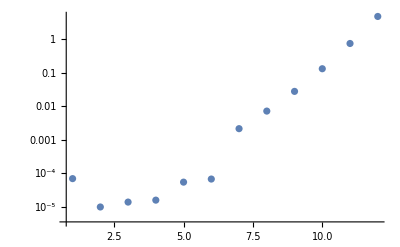

```mathematica
ListLogPlot[timeRuns,PlotRange-> All]
```

```mathematica
matrix3=N[matrix1];
Eigenvalues[matrix3]
Eigenvectors[matrix3]
```

{15.6092+0. ⅈ,-6.6161+0. ⅈ,-1.99657+0.443649 ⅈ,-1.99657-0.443649 ⅈ}

{{0.329458+0. ⅈ,0.59229+0. ⅈ,0.340794+0. ⅈ,0.651543+0. ⅈ},{0.153667+0. ⅈ,0.792304+0. ⅈ,-0.500396+0. ⅈ,-0.31344+0. ⅈ},{0.233237-0.386085 ⅈ,-0.193481+0.337534 ⅈ,-0.648307+0. ⅈ,0.451064+0.146335 ⅈ},{0.233237+0.386085 ⅈ,-0.193481-0.337534 ⅈ,-0.648307+0. ⅈ,0.451064-0.146335 ⅈ}}

Are the eigenvectors normalized?  Let's check:

```mathematica
eigvec=Eigenvectors[matrix3];
Table[eigvec[[i]].Conjugate[eigvec[[i]] ],{i,1,4}]
```

{1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ}

Pretty darn close!  Let's chop off anything less that 10^-10.

```mathematica
Table[Chop[eigvec[[i]].Conjugate[eigvec[[i]] ]],{i,1,4}]
```

{1.,1.,1.,1.}

Mathematica Gotchas

### Mathematica cares about Capitalization

Every function or command in Mathematica begins with a Capital Letter.  Any English word in the command will have an internal Capital Letter.  The function for a contour plot is ContourPlot, not Contourplot.  Mathematica will interpret any incorrect spelling or capitalization as a definition of some new command.  For example, only one of the following is correct.  Which one?

```mathematica
arcsin[1]
Arcsin[1]
ArcSin[1]
```

arcsin[1]

Arcsin[1]

π/2

### Mathematica is a symbolic manipulator.

What is the value of Sin[π/4] ?

```mathematica
a=Sin[π/4]
```

1/(√2)

Mathematica will keep this symbolic expression, unless you tell it to evaluate it as a number:

```mathematica
N[a]
```

0.707107

The two expressions below are not equivalent to Mathematica: one is a collection of symbols, and one is a number.

```mathematica
10/7
10./7
```

10/7

1.42857

### Mathematica never forgets

Mathematica remembers everything you've executed.  Even if you've deleted the cell or forgotten about the command, it will remember it (until you either restart the kernel or tell it explicitly to forget something).   Now, let's say you want to solve the quadratic equation:

```mathematica
Solve[{a x^2+b x+c ==0},{x}]
```

{{x→(-b-√(b^2-2 √2 c))/(√2)},{x→(-b+√(b^2-2 √2 c))/(√2)}}

Oops!  We don't get the quadratic formula.  We set a numerical value to "a" in the previous section.  We have to clear the value of "a"

```mathematica
Clear[a];
Solve[{a x^2+b x+c ==0},{x}]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

### Assignment versus equals

Look at the two expressions below.  The first assigns the value "0" to the variable "zero".  Whenever you type the variable name, Mathematica just substitutes in the value you assigned.  The second expression is an equation.  It is a logical relation.  It's not a rule for substitution, but a relationship that you can use in solving systems of equation.

```mathematica
zero=0
y1^2 + 3 == 0
```

0

3+y1^2==0

### Plotting against you

Mathematica can only plot numbers.  If any part of your expression is not defined, it won't be able to plot it.

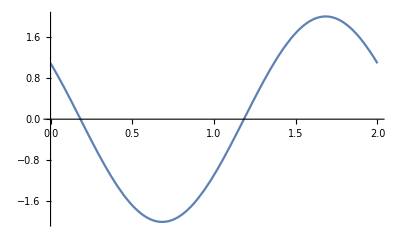

```mathematica
y=A Sin[k x-w t];
A=2;
k=π;
w=2;
t=5;
Plot[y,{x,0,2}]
```

Set the value of t above and then try it again.

### Variable blindness

If you don't leave spaces between your variables, Mathematica just assumes that this is some new variable.  Note that "mg" is not defined, but "m g" is defined.

```mathematica
m=2;
g = 9.8;
mg
m g
```

mg

19.6

## Combining Plots

The simplest way to combine 2D plots is to give them as a list to the plot command.

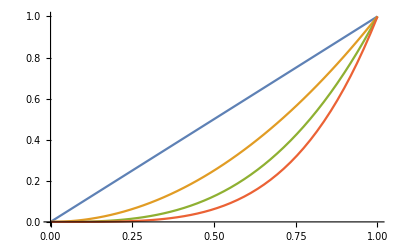

```mathematica
Plot[{x,x^2,x^3,x^4},{x,0,1}]
```

If you name individual plots, you can also combine them using Show.

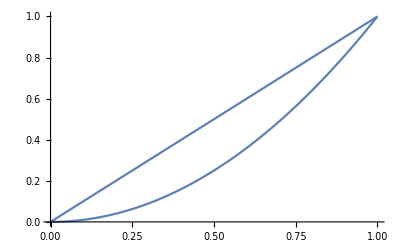

```mathematica
plt1=Plot[x,{x,0,1}];
plt2=Plot[x^2,{x,0,1}];
Show[plt1,plt2]
```

```mathematica
plt3=Plot3D[Sin[x y],{x,-π,π},{y,-π,π},PlotPoints->40]
plt4=Plot3D[Cos[x y],{x,-π,π},{y,-π,π},PlotPoints->40]
Show[plt3,plt4]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

## Differential Equations

### Simple ODE’s

```mathematica
eqn=D[x[t],t,t] + x[t] == 0
DSolve[eqn,x[t],t]
```

x[t]+x''[t]==0

{{x[t]→C[1] Cos[t]+C[2] Sin[t]}}

```mathematica
eqns={D[x[t],t,t] + x[t] == 0,x[0]==0, x[1]==1};
DSolve[eqns,x[t],t]
```

{{x[t]→Csc[1] Sin[t]}}

### Harder ODE’s

```mathematica
eqns={D[x[t],t,t]+ Cos[t] x[t]== 0, x[0]==0, x'[0]==1}
soln=DSolve[eqns,x[t],{t,0,16}]
```

{Cos[t] x[t]+x''[t]==0,x[0]==0,x'[0]==1}

{{x[t]→(2 MathieuS[0,-2,t/2])/MathieuSPrime[0,-2,0]}}

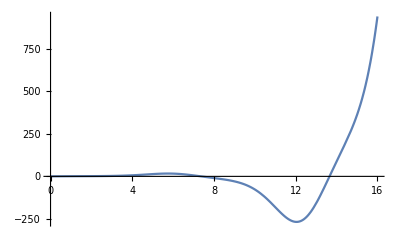

```mathematica
Plot[Evaluate[x[t]/.soln],{t,0,16},PlotRange->All]
```

### Non-linear DE’s

{Cos[t+x[t]]+t x[t]+x''[t]==0,x[0]==0,x'[0]==1}

{{x[t]→InterpolatingFunction[…][t]}}

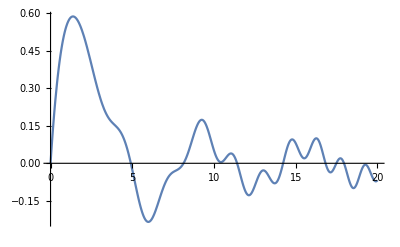

```mathematica
eqns={D[x[t],t,t]+ Cos[x[t]+t] +  t x[t] == 0, x[0]==0, x'[0]==1}
soln=NDSolve[eqns,x[t],{t,0,100}]
Plot[Evaluate[x[t]/.soln],{t,0,20},PlotRange->All]
```

## Solving a discretized problem:

If we want to solve the problem discussed in class, the electron in a harmonic oscillator, we need to construct the matrix, find the eigenvalues, and look at the results.

```mathematica
npts=20;
dx=1./(npts+1); 
hmat=Table[0,{i,1,npts},{j,1,npts}];
Do[hmat[[i,i]] = kappa(i dx -.5)^2  +2/dx^2,{i,1,npts}]
Do[hmat[[i,i+1]] =-1/dx^2,{i,1,npts-1}]
Do[hmat[[i+1,i]] =-1/dx^2,{i,1,npts-1}]
```

```mathematica
MatrixForm[hmat]
```

(882.+0.204649 kappa | -441. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-441. | 882.+0.163832 kappa | -441. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -441. | 882.+0.127551 kappa | -441. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -441. | 882.+0.095805 kappa | -441. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -441. | 882.+0.0685941 kappa | -441. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -441. | 882.+0.0459184 kappa | -441. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -441. | 882.+0.0277778 kappa | -441. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -441. | 882.+0.0141723 kappa | -441. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -441. | 882.+0.00510204 kappa | -441. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -441. | 882.+0.000566893 kappa | -441. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -441. | 882.+0.000566893 kappa | -441. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -441. | 882.+0.00510204 kappa | -441. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -441. | 882.+0.0141723 kappa | -441. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -441. | 882.+0.0277778 kappa | -441. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -441. | 882.+0.0459184 kappa | -441. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -441. | 882.+0.0685941 kappa | -441. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -441. | 882.+0.095805 kappa | -441. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -441. | 882.+0.127551 kappa | -441. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -441. | 882.+0.163832 kappa | -441.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -441. | 882.+0.204649 kappa)

```mathematica
hmatVal=hmat/. {kappa-> 0};
```

```mathematica
Eigenvalues[hmatVal]/π^2
```

{177.732,174.76,169.881,163.202,154.875,145.084,134.048,122.014,109.251,96.0436,82.687,69.4796,56.7165,44.6826,33.6469,23.8559,15.5282,8.84995,3.97025,0.998136}

```mathematica
npts=200;
dx=1./(npts+1); 
hmat=Table[0,{i,1,npts},{j,1,npts}];
Do[hmat[[i,i]] = kappa(i dx -.5)^2  +2/dx^2,{i,1,npts}]
Do[hmat[[i,i+1]] =-1/dx^2,{i,1,npts-1}]
Do[hmat[[i+1,i]] =-1/dx^2,{i,1,npts-1}]

hmatVal=hmat/. {kappa-> 0};
Eigenvalues[hmatVal]/π^2;
```

```mathematica
evecs=Eigenvectors[hmatVal];
```

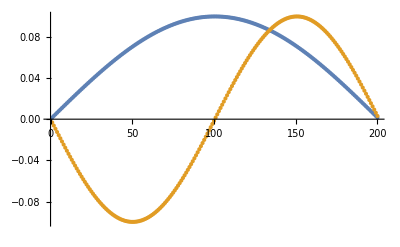

```mathematica
ListPlot[{evecs[[npts]],evecs[[npts-1]]}]
```

### Turn on the spring:

```mathematica
npts=200;
dx=1./(npts+1); 
hmat=Table[0,{i,1,npts},{j,1,npts}];
Do[hmat[[i,i]] = kappa(i dx -.5)^2  +2/dx^2,{i,1,npts}]
Do[hmat[[i,i+1]] =-1/dx^2,{i,1,npts-1}]
Do[hmat[[i+1,i]] =-1/dx^2,{i,1,npts-1}]

hmatVal=hmat/. {kappa-> 10000};
evals=Eigenvalues[hmatVal]
```

{163086.,163086.,162425.,162425.,161966.,161966.,161668.,161635.,161475.,161326.,161141.,160931.,160699.,160444.,160168.,159872.,159556.,159219.,158863.,158488.,158093.,157679.,157247.,156795.,156325.,155837.,155330.,154805.,154262.,153701.,153123.,152527.,151913.,151282.,150635.,149970.,149288.,148590.,147876.,147145.,146399.,145636.,144858.,144064.,143255.,142431.,141593.,140739.,139871.,138989.,138092.,137182.,136259.,135322.,134372.,133409.,132433.,131445.,130445.,129432.,128408.,127373.,126327.,125269.,124201.,123123.,122034.,120935.,119827.,118710.,117583.,116448.,115304.,114152.,112992.,111825.,110650.,109468.,108279.,107083.,105882.,104674.,103461.,102242.,101019.,99790.4,98557.7,97320.8,96080.1,94835.9,93588.4,92338.1,91085.1,89829.8,88572.5,87313.5,86053.1,84791.6,83529.4,82266.7,81003.8,79741.1,78478.9,77217.4,75957.,74698.,73440.7,72185.4,70932.4,69682.1,68434.6,67190.4,65949.7,64712.8,63480.1,62251.8,61028.2,59809.7,58596.5,57388.9,56187.3,54991.9,53803.,52620.9,51445.9,50278.2,49118.2,47966.2,46822.4,45687.1,44560.6,43443.1,42335.,41236.5,40147.9,39069.4,38001.3,36943.8,35897.3,34862.,33838.1,32825.9,31825.6,30837.5,29861.8,28898.8,27948.6,27011.6,26088.,25177.9,24281.6,23399.4,22531.4,21677.8,20838.9,20014.9,19206.,18412.3,17634.1,16871.6,16124.9,15394.3,14679.8,13981.8,13300.4,12635.7,11987.9,11357.2,10743.7,10147.7,9569.17,9008.38,8465.47,7940.58,7433.85,6945.46,6475.54,6024.26,5591.77,5178.26,4783.89,4408.86,4053.39,3717.69,3402.,3106.46,2831.06,2575.3,2337.72,2115.46,1904.39,1700.01,1498.83,1298.8,1099.08,899.368,699.613,499.799,299.923,99.9845}

Let’s see if the scaling we thought was correct for the eigenvalues is actually correct.

```mathematica
evals/√10000
```

{1630.86,1630.86,1624.25,1624.25,1619.66,1619.66,1616.68,1616.35,1614.75,1613.26,1611.41,1609.31,1606.99,1604.44,1601.68,1598.72,1595.56,1592.19,1588.63,1584.88,1580.93,1576.79,1572.47,1567.95,1563.25,1558.37,1553.3,1548.05,1542.62,1537.01,1531.23,1525.27,1519.13,1512.82,1506.35,1499.7,1492.88,1485.9,1478.76,1471.45,1463.99,1456.36,1448.58,1440.64,1432.55,1424.31,1415.93,1407.39,1398.71,1389.89,1380.92,1371.82,1362.59,1353.22,1343.72,1334.09,1324.33,1314.45,1304.45,1294.32,1284.08,1273.73,1263.27,1252.69,1242.01,1231.23,1220.34,1209.35,1198.27,1187.1,1175.83,1164.48,1153.04,1141.52,1129.92,1118.25,1106.5,1094.68,1082.79,1070.83,1058.82,1046.74,1034.61,1022.42,1010.19,997.904,985.577,973.208,960.801,948.359,935.884,923.381,910.851,898.298,885.725,873.135,860.531,847.916,835.294,822.667,810.038,797.411,784.789,772.174,759.57,746.98,734.407,721.854,709.324,696.821,684.346,671.904,659.497,647.128,634.801,622.518,610.282,598.097,585.965,573.889,561.873,549.919,538.03,526.209,514.459,502.782,491.182,479.662,468.224,456.871,445.606,434.431,423.35,412.365,401.479,390.694,380.013,369.438,358.973,348.62,338.381,328.259,318.256,308.375,298.618,288.988,279.486,270.116,260.88,251.779,242.816,233.994,225.314,216.778,208.389,200.149,192.06,184.123,176.341,168.716,161.249,153.943,146.798,139.818,133.004,126.357,119.879,113.572,107.437,101.477,95.6917,90.0838,84.6547,79.4058,74.3385,69.4546,64.7554,60.2426,55.9177,51.7826,47.8389,44.0886,40.5339,37.1769,34.02,31.0646,28.3106,25.753,23.3772,21.1546,19.0439,17.0001,14.9883,12.988,10.9908,8.99368,6.99613,4.99799,2.99923,0.999845}

Now we can plot the lowest two energy eigenvectors.   Remember that Mathematica calculates them in order of decreasing absolute value of the eigenvalues.  Therefore our last two eigenvectors are the lowest two eigenstates.

```mathematica
evecs=Eigenvectors[hmatVal];
```

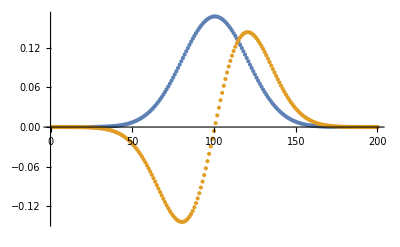

```mathematica
ListPlot[{evecs[[npts]],evecs[[npts-1]]}]
```

Finally, let’s sweep the spring constant and see when we switch over from infinite square well energies to harmonic oscillator energies.  First we will calculate all of the eigenvalues.  Then we’ll pick out the ones we want.

```mathematica
maxn=15;
allEvals=Table[hmatVal=(hmat/. kappa-> 2^n);
Eigenvalues[hmatVal],{n,0,maxn}];
```

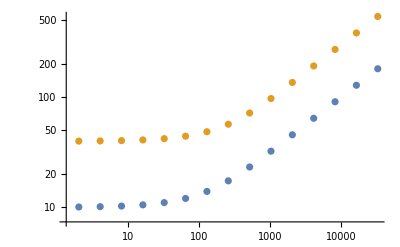

```mathematica
list1=Table[{2^n,allEvals[[n+1,npts]]},{n,1,maxn}];
list2=Table[{2^n,allEvals[[n+1,npts-1]]},{n,1,maxn}];
ListLogLogPlot[{list1,list2}]
```

Ok, we see that it switches behavior around κ = 100.  Can we see how it depends on κ?  First we need to take the logarithm of the x and y points.

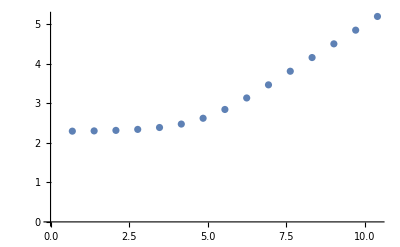

```mathematica
logList1=Log[list1];
ListPlot[logList1]
```

Next, we need to get the last few of them, where it’s linear.

```mathematica
data=Take[logList1,-6]
```

{{Log[1024],3.46767},{Log[2048],3.81233},{Log[4096],4.15879},{Log[8192],4.50532},{Log[16384],4.85183},{Log[32768],5.19832}}

Now we fit is to a line:

```mathematica
Fit[data,{1,x},x]
```

0.00441055+0.499515 x

## Solving an iterative problem:

Recall our discusion of solving the 1D problem:

	y’ = - c y  
	y(0) = 1
	
The Euler method yields:

	y_(i+1)= y_i - c Δt y_i  
Let’s test this with c = 4 and Δt = .1   

Below I iterate the problem forward in time, saving the answers in a list, euler.  I then generate plots for the list and the exact answer,  Exp[- c t], but I don’t display either plot.  After that, I use the Show command to display both plots in the same frame.

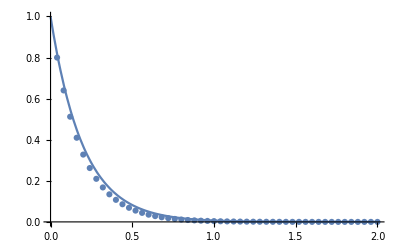

```mathematica
yold=1.;
c = 5.;
npts=50;
dt = 2.0/npts;
euler=Table[ynew= (1- c dt) yold ;  
yold= ynew; {i dt, yold},{i,1,npts}];
eulerPlot=ListPlot[euler,PlotRange-> All];
exactPlot=Plot[Exp[- c t],{t,0,2},PlotRange-> All];
Show[eulerPlot,exactPlot,PlotRange-> All]
```

Try running the routines below, changing npts to lower and lower values.

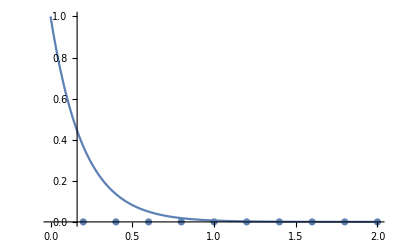

```mathematica
yold=1.;
c = 5.;
npts=10;
dt = 2.0/npts;
euler=Table[ynew= (1- c dt) yold ;  
yold= ynew; {i dt, yold},{i,1,npts}];
eulerPlot=ListPlot[euler,PlotRange-> All];
exactPlot=Plot[Exp[- c t],{t,0,2},PlotRange-> All];
Show[eulerPlot,exactPlot,PlotRange-> All]
```

Now let’s try an implicit scheme.  Note that it is always stable.  However, it is not always accurate.

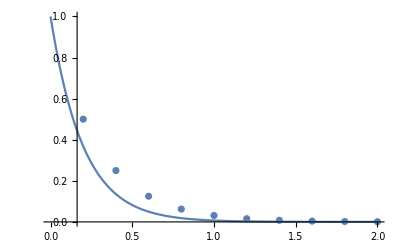

```mathematica
yold=1.;
c = 5.;
npts=10;
dt = 2.0/npts;
euler=Table[ynew= yold/(1+ c dt) ;  
yold= ynew; {i dt, yold},{i,1,npts}];
eulerPlot=ListPlot[euler,PlotRange-> All];
exactPlot=Plot[Exp[- c t],{t,0,2},PlotRange-> All];
Show[eulerPlot,exactPlot,PlotRange-> All]
```

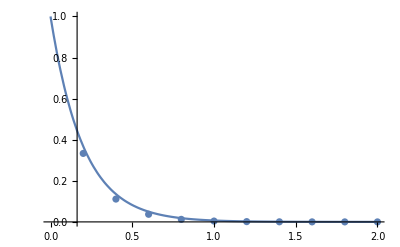

```mathematica
yold=1.;
c = 5.;
npts=10;
dt = 2.0/npts;
euler=Table[ynew= yold (1- c/2 dt)/(1+ c/2 dt) ;  
yold= ynew; {i dt, yold},{i,1,npts}];
eulerPlot=ListPlot[euler,PlotRange-> All];
exactPlot=Plot[Exp[- c t],{t,0,2},PlotRange-> All];
Show[eulerPlot,exactPlot,PlotRange-> All]
```

Let’s compare them all:

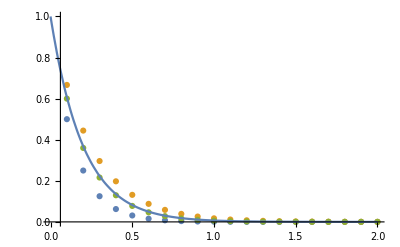

```mathematica
yold=1.;
c = 5.;
npts=20;
dt = 2.0/npts;
eulerForward=Table[ynew= (1- c dt) yold ;  
yold= ynew; {i dt, yold},{i,1,npts}];
yold=1.;
eulerBackward=Table[ynew= yold/(1+ c dt) ;  
yold= ynew; {i dt, yold},{i,1,npts}];
yold=1.;
eulerMidpoint=Table[ynew= yold (1- c/2 dt)/(1+ c/2 dt) ;  
yold= ynew; {i dt, yold},{i,1,npts}];
eulerPlot=ListPlot[{eulerForward, eulerBackward,eulerMidpoint},PlotRange-> All];
exactPlot=Plot[Exp[- c t],{t,0,2},PlotRange-> All];
Show[eulerPlot,exactPlot,PlotRange-> All]
```

Why does the midpoint approach work the best?    Well, in each time step we are approximating e^(-c dt).   The exact answer is:

```mathematica
Clear[c, dt];
Series[Exp[-c dt],{dt, 0, 6}]
```

1-c dt+(c^2 dt^2)/2-(c^3 dt^3)/6+(c^4 dt^4)/24-(c^5 dt^5)/120+(c^6 dt^6)/720+O[dt]^7

Let's look at how well they do. The forward Euler approximates it by (1 - c*dt).   It has no higher order terms.  The backward approximates it by:

```mathematica
Series[1/(1+c dt),{dt,0,6}]
```

1-c dt+c^2 dt^2-c^3 dt^3+c^4 dt^4-c^5 dt^5+c^6 dt^6+O[dt]^7

The above series has the dt^2 term, but too much of it.

```mathematica
Series[(1- c/2 dt)/(1+ c/2 dt), {dt,0,6}]
```

1-c dt+(c^2 dt^2)/2-(c^3 dt^3)/4+(c^4 dt^4)/8-(c^5 dt^5)/16+(c^6 dt^6)/32+O[dt]^7

The midpoint form has exactly the right amount to order dt^2